# Problem 2, Discrete growth models

## for February 09, 23.59, 2024

## Assume that the population size depends on discrete time (τ = 0,1,2,...) as follows Here, the parameters satisfy: , , and .

## a) Analytically determine the non-negative steady states (fixed points) of the model (2).

There is a trivial fixed point at , and there is a fixed point at , which can be found by setting  and solving for .

## b) Perform linear stability analysis and discuss how the linear stability of the non-negative steady states depends on the parameters.

To solve this one needs to take the derivative of the growth model which corresponds to:
 
Now insert the  and the resulting derivative is:

Now insert the  and the resulting derivative is:


In general, for non-negative fixed points it follows that if  then the fixed point is stable and if  then the fixed point is unstable. 


With the given criterion’s for  and  one can see that the stable point at  is always going to be unstable. 

The analysis is a little more complex for the second stable point  . 
If one inserts  to the solution one can see that the fixed point will always be stable for the parameters given because . 

It can be observed that there is a critical point at , where the stability changes from stable to unstable or vice versa. Thus one can analyse where  and one finds that this happens when  and when  or  which is not possible due to the restrictions on the parameters. So there are infinitely many options on where a bifurcation from a stable to a unstable steady state happens. 
But one thing that can be said about the stability is dependent upon . 
	If  leads to  (stable steady state)  
	If  leads to  (unstable steady state).

## c) Analytically find all conditions on the parameters (within their ranges of validity) where a bifurcation from a stable steady state to an unstable steady state occurs.

See b).

## In the following, use the parameter values: and . d) Investigate how the population size depends on time for the following values of the initial population size: and 10. For each case, use the linear stability analysis performed in task b) to approximate the population dynamics in the vicinity of the unstable steady state. [Hint: treat the initial condition as a small perturbation around the unstable steady state, and plot how this perturbation, and consequently the population size, is expected to change over time according to the linear stability analysis.] Plot this approximation together with the corresponding (exact) population dynamics obtained by iterating Eq. (2). Use log-log scale for plotting to distinguish well between the different curves.

As already hinted at in sub task b) the fixed point in question must be stable due to the fact that , and thus the derivative of the growth will remain negative for all values of . One can see the behaviour in the following plots in red and the approximation of the linear stability analysis

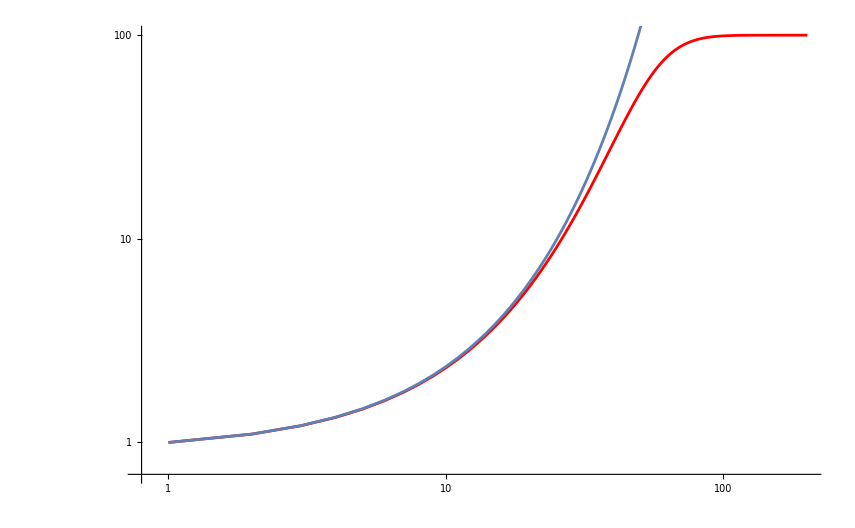

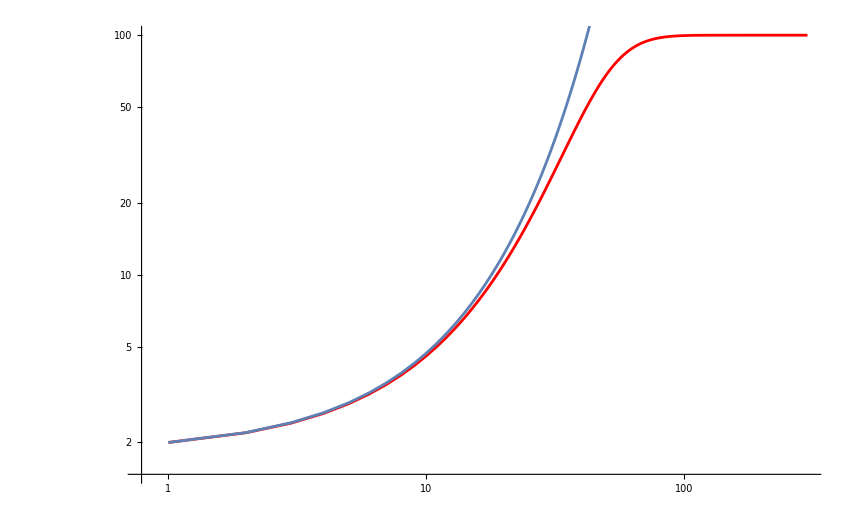

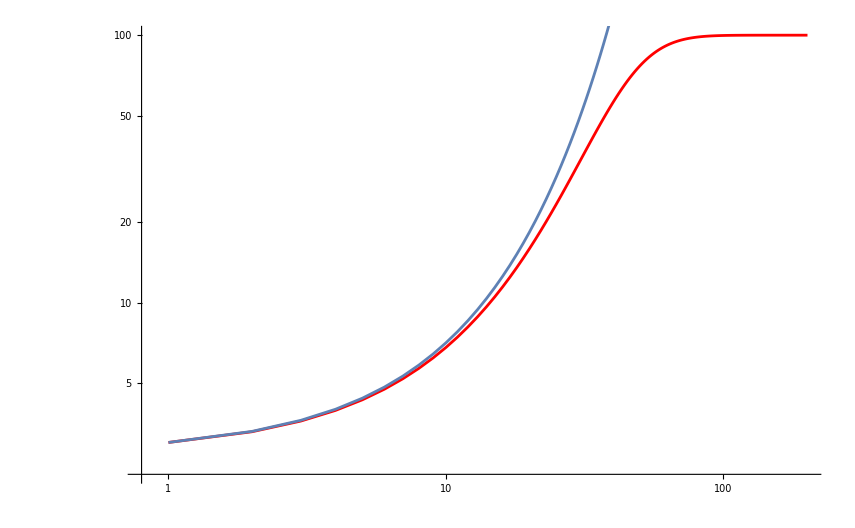

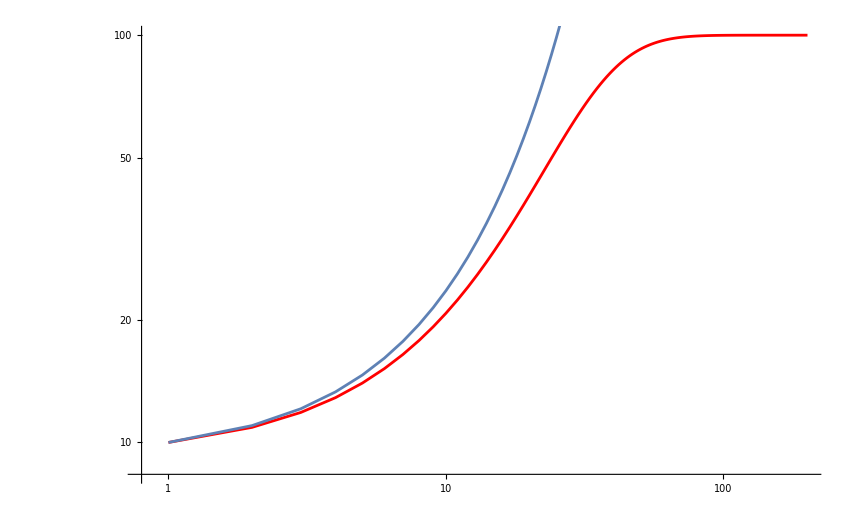

```mathematica
ClearAll["Global`*"];
b = 1;
k = 10^3;
r = 0.1;

data1 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {1}, 200];
data2 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {2}, 300];
data3 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {3}, 200];
data4 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {10}, 200];

pairedData1 = MapIndexed[{First[#2], #[[1]]} &, data1];
pairedData2 = MapIndexed[{First[#2], #[[1]]} &, data2];
pairedData3 = MapIndexed[{First[#2], #[[1]]} &, data3];
pairedData4 = MapIndexed[{First[#2], #[[1]]} &, data4];

data11 = NestList[{#[[1]]*(r+1)} &, {1}, 200];
data22 = NestList[{#[[1]]*(r+1)} &, {2}, 200];
data33 = NestList[{#[[1]]*(r+1)} &, {3}, 200];
data44 = NestList[{#[[1]]*(r+1)} &, {10}, 200];

pairedData11 = MapIndexed[{First[#2], #[[1]]} &, data11];
pairedData22 = MapIndexed[{First[#2], #[[1]]} &, data22];
pairedData33 = MapIndexed[{First[#2], #[[1]]} &, data33];
pairedData44 = MapIndexed[{First[#2], #[[1]]} &, data44];

Plot11 = ListLogLogPlot[{pairedData11},Joined->True];
Plot22 = ListLogLogPlot[{pairedData22},Joined->True];
Plot33 = ListLogLogPlot[{pairedData33},Joined->True];
Plot44 = ListLogLogPlot[{pairedData44},Joined->True];

Plot1 = ListLogLogPlot[{pairedData1}, PlotLabel -> "",Joined -> True,PlotStyle->Red];
Plot2 = ListLogLogPlot[{pairedData2}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Plot3 = ListLogLogPlot[{pairedData3}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Plot4 = ListLogLogPlot[{pairedData4}, PlotLabel -> "", Joined -> True,PlotStyle->Red];

Show[Plot1,Plot11]
Show[Plot2,Plot22]
Show[Plot3,Plot33]
Show[Plot4,Plot44]
```

## e) Discuss how well the stability analysis approximates the exact dynamics. How does the initial condition influence the approximation?

The stability analysis approximates the good in the beginning ok especially for small perturbations from the unstable fixed point. But with increasing steps they become worse. This is because the Tylor approximation is an unbounded function.

## f) Use linear stability analysis to approximate the dynamics in the vicinity of the stable steady state. Use initial population size , where is the value of the stable steady state and is an initial perturbation around . Choose and 10. Proceed as follows. Starting from an initial perturbation , approximate the dynamics until the system comes close to using the linear stability analysis around the stable steady state. Plot this approximation together with the exact dynamics, starting at . Perform the approximation for the different values of the initial perturbation . How does the initial perturbation influence the approximation?

100.

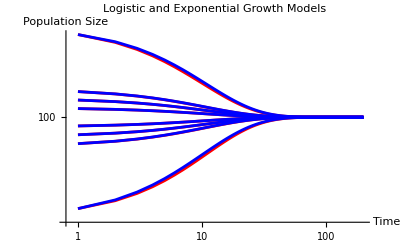

```mathematica
ClearAll["Global`*"];
k = 10^3;
r = 0.1;
b = 1;
fixedPoint = k*r^(1/b)
(* Generate logistic growth data *)
data1 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint+1}, 200];
data2 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint+2}, 200];
data3 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint+3}, 200];
data4 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint+10}, 200];
data5 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint-1}, 200];
data6 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint-2}, 200];
data7 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint-3}, 200];
data8 = NestList[{((r + 1)*#[[1]])/(1 + (#[[1]]/k)^b)} &, {fixedPoint-10}, 200];

(* Pair time steps with data *)
pairedData1 = MapIndexed[{First[#2], #[[1]]} &, data1];
pairedData2 = MapIndexed[{First[#2], #[[1]]} &, data2];
pairedData3 = MapIndexed[{First[#2], #[[1]]} &, data3];
pairedData4 = MapIndexed[{First[#2], #[[1]]} &, data4];
pairedData5 = MapIndexed[{First[#2], #[[1]]} &, data5];
pairedData6 = MapIndexed[{First[#2], #[[1]]} &, data6];
pairedData7 = MapIndexed[{First[#2], #[[1]]} &, data7];
pairedData8 = MapIndexed[{First[#2], #[[1]]} &, data8];

data11 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint-1}, 200];
data22 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint-2}, 200];
data33 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint-3}, 200];
data44 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint-10}, 200];
data55 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint+1}, 200];
data66 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint+2}, 200];
data77 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint+3}, 200];
data88 = NestList[{((1+r)(b*k(r^(1/b))^(1+b)+#[[1]](1+(r^(1/b))^b-b(r^(1/b))^b)))/((1+(r^(1/b))^b)^2)} &, {fixedPoint+10}, 200];


pairedData11 = MapIndexed[{First[#2], #[[1]]} &, data11];
pairedData22 = MapIndexed[{First[#2], #[[1]]} &, data22];
pairedData33 = MapIndexed[{First[#2], #[[1]]} &, data33];
pairedData44 = MapIndexed[{First[#2], #[[1]]} &, data44];
pairedData55 = MapIndexed[{First[#2], #[[1]]} &, data55];
pairedData66 = MapIndexed[{First[#2], #[[1]]} &, data66];
pairedData77 = MapIndexed[{First[#2], #[[1]]} &, data77];
pairedData88 = MapIndexed[{First[#2], #[[1]]} &, data88];

Plot11 = ListLogLogPlot[{pairedData11},Joined->True];
Plot22 = ListLogLogPlot[{pairedData22},Joined->True];
Plot33 = ListLogLogPlot[{pairedData33},Joined->True];
Plot44 = ListLogLogPlot[{pairedData44},Joined->True];

ListLogLogPlot[
  {pairedData1, pairedData2, pairedData3, pairedData4, pairedData5, pairedData6, pairedData7, pairedData8,
  pairedData11, pairedData22, pairedData33, pairedData44, pairedData55, pairedData66, pairedData77, pairedData88},
  Joined -> True, 
  PlotStyle -> {Red, Red, Red, Red, Red, Red, Red, Red, Blue, Blue, Blue, Blue, Blue, Blue, Blue, Blue},
  PlotLabel -> "Logistic and Exponential Growth Models",
  AxesLabel -> {"Time", "Population Size"},
  ImageSize->Full
]
```

The second approximation around the fixed point is . This with the parameters applied it simplifies to   which approximates the behaviour very well because of the stabilising second term.